## CLIPedia Inference

Published by Agostino Nickl, 2025, under the MIT License, in tandem with the paper Nickl, Agostino, “Navigating CLIPedia: Architectonic Instruments for Querying and Questing a Latent Encyclopedia,” Frontiers of Architectural Research (forthcoming). CLIPedia was written and tested in Mathematica 13.2 on Mac. For more information, refer to the paper and the README.md.

#### Load Dependencies

Clipedia runs with a tiny subset of its corpus for demo purposes. Any change to the pre-determined parameters will lead to file errors. You can request the full corpus from the author as listed in the README, or build your own CLIPedia.

```mathematica
(*1. Set the root folder of the CLIPedia repository*)
$repoFolder=SystemDialogInput["Directory"]
```

```mathematica
(*2. Set a local folder for exports*)
exportFolder=SystemDialogInput["Directory"]
```

```mathematica
(*3. Evaluate all initialization functions by clicking yes on the notebook pop-up*)
functions=NotebookOpen[FileNameJoin[{$repoFolder,"code","clipedia_functions.nb"}],Visible->True];
SelectionMove[functions,Before,Notebook];SelectionMove[functions,Next,Cell];SelectionEvaluate[functions];
```

CLIPedia requires OpenCLIP to work. If you haven’t done so already, the next step will download the OpenCLIP models from the Wolfram Net Repository. By proceeding, you accept OpenClip’s license and terms. OpenCLIP was published with a paper by M. Cherti, R. Beaumont, R. Wightman, M. Wortsman, G. Ilharco, C. Gordon, C. Schuhmann, L. Schmidt, J. Jitsev, "Reproducible Scaling Laws for Contrastive Language–Image Learning," arXiv:2212.07143 (2022).

```mathematica
(*4. If not done so already, download OpenCLIP models*)
DownloadCLIP[$repoFolder];
```

```mathematica
(*5. Load Clipedia Setup (Demo Only)*)
LoadClipediaSetup[$repoFolder];
```

## Querying

#### Simple Query

AskClipedia returns the best matching elements from the Wikipedia corpus to queries expressed in natural language or through images .

```mathematica
(*1st argument: query string or image, 2nd: desired mode, txt or img, 3rd: number of results*)
AskCLIPedia["Search for the Parthenon","img" ,4]
```

{[-Graphics-](https://en.wikipedia.org/wiki?curid=525098),[-Graphics-](https://en.wikipedia.org/wiki?curid=38005076),[-Graphics-](https://en.wikipedia.org/wiki?curid=23672),[-Graphics-](https://en.wikipedia.org/wiki?curid=34839)}

#### Advanced Queries

Advanced queries allow to exert more control on inference parameters, and to play with functions such as automatic compilations of reference lists .

```mathematica
(*1. Set Query Parameters*)
query=-Graphics-; (*Query with a string or an image*)
mode="txt"; (*Desired answer modality*)
results=10; (*Desired number of results*)
imgRCS=0.02; (*Ranked corpus sampling parameter – how many img results are screened*)
txtRCS=0.002;(*Ranked corpus sampling parameter – how many text results are screened*)
```

```mathematica
(*2. Retrieve BMEs from SOM, enrich with Metadata, and display as list*)
queryElem=ClipEncode[query,imgModel,textModel];
queryResults=QueryEnSOM[clipedia,queryElem[["vector_ref"]],mode,imgRCS, txtRCS,results,$repoFolder];
queryAssoc=Table[AddInfo[CollateEnAssoc[queryResults[[i]]]],{i,Length@queryResults}];
ListResults[queryAssoc]
```

{Due to the changes in location and leadership, the Bauhaus school's artistic and political objectives continuously shifted, which contributed to the school's financial instability. Due to the increasing political pressure of the anti-modernist Nazi government, the Bauhaus shut its doors in 1933.^ℹhttps://en.wikipedia.org/wiki?curid=53699392Nonehttps://en.wikipedia.org/wiki?curid=53699392Hyperlink0.5,"Bauhaus and its Sites in Weimar, Dessau and Bernau" is a World Heritage Site in Germany, comprising six separate sites which are associated with the Bauhaus art school. It was designated in 1996 with four initial sites, and in 2017 two further sites were added.[1]https://whc.unesco.org/en/list/729Nonehttps://whc.unesco.org/en/list/729Hyperlink0.5^ℹhttps://en.wikipedia.org/wiki?curid=59524982Nonehttps://en.wikipedia.org/wiki?curid=59524982Hyperlink0.5,The building was constructed between 1925 and 1926 according to plans by Walter Gropius as a school building for the Bauhaus School of Art, Design and Architecture.[2] The building itself and the Masters' Houses that were built in the immediate vicinity established the reputation of the Bauhaus as an "icon of modernism".Citation needed^ℹhttps://en.wikipedia.org/wiki?curid=16652143Nonehttps://en.wikipedia.org/wiki?curid=16652143Hyperlink0.5,The Bauhaus was founded in Weimar in 1919 by Walter Gropius and remained there until 1925 when it moved to Dessau due to political pressure.[4]https://www.uni-weimar.de/en/university/profile/portrait/history/Nonehttps://www.uni-weimar.de/en/university/profile/portrait/history/Hyperlink0.5 It was housed in two neighbouring buildings that had previously been two separate art schools, both designed in the Art Nouveau style by Henry van de Velde. These are:^ℹhttps://en.wikipedia.org/wiki?curid=59524982Nonehttps://en.wikipedia.org/wiki?curid=59524982Hyperlink0.5,The Bauhaus and its Sites in Weimar, Dessau and Bernau World Heritage Site comprises six separate sites, two in Weimar, which are associated with the Bauhaus art school, which had a revolutionary influence on 20th century architectural and aesthetic thinking and practice.^ℹhttps://en.wikipedia.org/wiki?curid=47198Nonehttps://en.wikipedia.org/wiki?curid=47198Hyperlink0.5,The two visited the Bauhaus in Dessau together. At the time Ruhtenberg was a public relations aide to designer Bruno Paul.[3] Johnson, working with Henry-Russell Hitchcock, was gathering material for "The International Style: Architecture Since 1922." Ruhtenberg was traveling with them.[4]^ℹhttps://en.wikipedia.org/wiki?curid=9081217Nonehttps://en.wikipedia.org/wiki?curid=9081217Hyperlink0.5,"Bauhaus Dessau", also "Bauhaus-Building Dessau", is a building-complex in Dessau-Roßlau. It is considered the pinnacle of pre-war modern design in Europe and originated out of the dissolution of the Weimar School and the move by local politicians to reconcile the city's industrial character with its cultural past.[1]^ℹhttps://en.wikipedia.org/wiki?curid=16652143Nonehttps://en.wikipedia.org/wiki?curid=16652143Hyperlink0.5,The world renowned Bauhaus design school was founded in 1919 in the city of Weimar,[88]https://www.bauhaus-2019.de/cms/website.php?id=/en/index.htmNonehttps://www.bauhaus-2019.de/cms/website.php?id=/en/index.htmHyperlink0.5 approximately 0 from Erfurt, 12 minutes by train. The buildings are now part of a World Heritage Site and are today used by the Bauhaus-Universität Weimar, which teaches design, arts, media and technology related subjects.Citation needed^ℹhttps://en.wikipedia.org/wiki?curid=9481Nonehttps://en.wikipedia.org/wiki?curid=9481Hyperlink0.5,(Fig.1)https://en.wikipedia.org/wiki/File:Bauhaus.JPGNonehttps://en.wikipedia.org/wiki/File:Bauhaus.JPGHyperlink0.5The "Bauhaus Dessau Foundation" is a nonprofit organization devoted to research and teaching in the field of experimental design. It was founded by the German Federal Government in 1994 and is based in the Bauhaus Dessau building in the state of Saxony-Anhalt. Its staff includes architects, town planners, sociologists, cultural scientists, artists, and art historians.^ℹhttps://en.wikipedia.org/wiki?curid=25727674Nonehttps://en.wikipedia.org/wiki?curid=25727674Hyperlink0.5,Apart from the permanent exhibition, each year there are about four special exhibitions. There are also lectures, workshops and discussions, exhibitions in the sculpture yard, readings and concerts. The Bauhaus Archive in Berlin has long held the only official Bauhaus trademark label to reproduce a limited number of Bauhaus designs.^ℹhttps://en.wikipedia.org/wiki?curid=5089715Nonehttps://en.wikipedia.org/wiki?curid=5089715Hyperlink0.5}

```mathematica
(*3. Create a QueryBook with all results*)
ClipediaLog[queryAssoc,queryElem[["query"]],exportFolder];
```

```mathematica
(*4. Show all text references in results - txt mode queries only*)
ShowTextReferences[queryAssoc]
```

https://whc.unesco.org/en/list/729, Bauhaus and its Sites in Weimar, Dessau and Bernau, UNESCO World Heritage Centre, United Nations Educational, Scientific, and Cultural Organization, 29 December 2018
Kleiner, Fred S., Gardner's Art through the Ages: The Western Perspective, Volume II, Cengage Learning, 2020, 978-0-357-37046-9, Boston, MA, 928, en
https://www.uni-weimar.de/en/university/profile/portrait/history/ Bauhaus-Universität Weimar. History. Retrieved 29 December 2019
Schulze, Franz.  "Philip Johnson: Life and Work".  Chicago: University of Chicago Press, 1994, 54-55.
Schulze, Franz.  "Philip Johnson: Life and Work."  Chicago: University of Chicago Press, 1994, 67
Pottgiesser, Uta, Reglazing Modernism: Intervention Strategies for 20th-Century Icons, Ayón, Angel, Richards, Nathaniel, Birkhäuser, 2019, 978-3-0356-1934-8, Basel, 196
https://www.bauhaus-2019.de/cms/website.php?id=/en/index.htm Bauhaus 2019. The Bauhaus in Thuringia.  Retrieved 19 November 2016

```mathematica
(*5. Find all associated images - txt mode queries only*)
queryImageAssoc=CollateTextImgAssoc[queryResults];
ListResults[queryImageAssoc]
```

{[-Graphics-](https://en.wikipedia.org/wiki?curid=59524982),[-Graphics-](https://en.wikipedia.org/wiki?curid=16652143),[-Graphics-](https://en.wikipedia.org/wiki?curid=16652143),[-Graphics-](https://en.wikipedia.org/wiki?curid=16652143),[-Graphics-](https://en.wikipedia.org/wiki?curid=25727674)}

```mathematica
(*6. Compare with image BMEs from SOM for same query*)
mode="img";
queryResults=QueryEnSOM[clipedia,queryElem[["vector_ref"]],mode,imgRCS, txtRCS,results,$repoFolder];
queryAssoc=Table[AddInfo[CollateEnAssoc[queryResults[[i]]]],{i,Length@queryResults}];
ListResults[queryAssoc]
```

{[-Graphics-](https://en.wikipedia.org/wiki?curid=33687),[-Graphics-](https://en.wikipedia.org/wiki?curid=25727674),[-Graphics-](https://en.wikipedia.org/wiki?curid=16652143),[-Graphics-](https://en.wikipedia.org/wiki?curid=149281),[-Graphics-](https://en.wikipedia.org/wiki?curid=60355116),[-Graphics-](https://en.wikipedia.org/wiki?curid=5356555),[-Graphics-](https://en.wikipedia.org/wiki?curid=12211450),[-Graphics-](https://en.wikipedia.org/wiki?curid=17660517),[-Graphics-](https://en.wikipedia.org/wiki?curid=832350),[-Graphics-](https://en.wikipedia.org/wiki?curid=17582340)}

## Questing

#### Orthodromes

Orthodromes plot a great circle through the unit sphere of CLIP, between point A, its antipode C, and B as a point in between.

```mathematica
(*1. Compute and display an Orthodrome between two queries*)
queryA="Column Capital"; (*Start point, string or image*)
queryB="Frieze"; (*End point, string or image*)
method="Orthodrome"; (*Method: Orthodrome, Slerp, or Linear Interpolation*)
crop=False; (*Whether Orthodromes should be cropped at destination*)
steps=8; (*Amount of interpolation steps*)
queryElemA=ClipEncode[queryA,imgModel,textModel];
queryElemB=ClipEncode[queryB,imgModel,textModel];
interpolatedVectors=InterpolateVectors[queryElemA[["vector_ref"]],queryElemB[["vector_ref"]],steps,method,crop,1];
Monitor[encounters=Table[Merge[{
AddInfo@CollateEnAssoc[QueryEnSOM[clipedia,interpolatedVectors[[i]],"img",0.01,0.0005,1,$repoFolder][[1]]]},First]
,{i,Length@interpolatedVectors}];,i];
queryLinks="https://en.wikipedia.org/wiki?curid="<>First[StringSplit[#[["imgID"]],"_"]]&/@encounters;
uniPos=FindLastUniquePositions[ColorConvert[#,"RGB"]&/@encounters[[All,"img"]]];
imgGrid=ShowLinearGuideImages[encounters[[uniPos,"img"]],4,3,queryLinks[[uniPos]],encounters[[uniPos,"imgTitle"]],2,2,200]
```

[-Graphics-](https://en.wikipedia.org/wiki?curid=5074285) | [-Graphics-](https://en.wikipedia.org/wiki?curid=42820744) | [-Graphics-](https://en.wikipedia.org/wiki?curid=3556314)
[-Graphics-](https://en.wikipedia.org/wiki?curid=2432705) | [-Graphics-](https://en.wikipedia.org/wiki?curid=2593853) | [-Graphics-](https://en.wikipedia.org/wiki?curid=343908) | [-Graphics-](https://en.wikipedia.org/wiki?curid=10615004)

```mathematica
(*2. Create a QueryBook with all results*)
ClipediaLog[encounters,"From "<>queryElemA[["query"]]<>" to "<>queryElemB[["query"]],exportFolder];
```

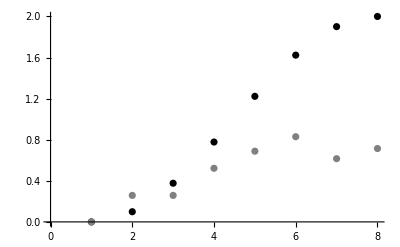

```mathematica
(*3. Make a plot showing distances relative to the first point, between calculated and concrete results*)
distances1=CosineDistance[interpolatedVectors[[1]],#]&/@interpolatedVectors;
distances2=CosineDistance[encounters[[All,"vector_ref"]][[1]],#]&/@encounters[[All,"vector_ref"]];
ListPlot[{distances1,distances2},PlotRange->{{0,Automatic},{0,2}},Axes->{False,True},PlotRangePadding->Scaled[.05],PlotStyle->{Black,Gray}]
```

Note: All functions below have stochastic components and fail without full corpus.  Request it from the author or build your own CLIPedia.

#### Diadromes

Diadromes are stochastic great circles, with a circular SOM seeking out paths connecting two points .

```mathematica
(*1. Compute and display a SOM-based Diadrome between two queries*)
queryA= "Column Capital";(*Start point, string or image*)
queryB="Frieze";(*End point, string or image*)
size=100; (*Size of connecting SOM*)
imgRCS=0.01; (*How many img results are screened*)
txtRCS=0.002;(*How many text results are screened*)
queryElemA=ClipEncode[queryA,imgModel,textModel];
queryElemB=ClipEncode[queryB,imgModel,textModel];
vecResults=({#[[5]],#[[4]]}&/@QueryEnSOM[clipedia,#[["vector_ref"]],"img",imgRCS, txtRCS,size,$repoFolder])&/@{queryElemA,queryElemB};
diadromes=InterpolateWithSOM[queryElemA[["vector_ref"]],queryElemB[["vector_ref"]],vecResults,30,2];
RenderImgRow[diadromes[[1]],100]
```

[-Graphics-](https://en.wikipedia.org/wiki?curid=5074285)[-Graphics-](https://en.wikipedia.org/wiki?curid=17936995)[-Graphics-](https://en.wikipedia.org/wiki?curid=823229)[-Graphics-](https://en.wikipedia.org/wiki?curid=3416422)[-Graphics-](https://en.wikipedia.org/wiki?curid=15467662)[-Graphics-](https://en.wikipedia.org/wiki?curid=7006345)[-Graphics-](https://en.wikipedia.org/wiki?curid=30717766)[-Graphics-](https://en.wikipedia.org/wiki?curid=2969846)[-Graphics-](https://en.wikipedia.org/wiki?curid=74277406)[-Graphics-](https://en.wikipedia.org/wiki?curid=59173216)[-Graphics-](https://en.wikipedia.org/wiki?curid=355024)[-Graphics-](https://en.wikipedia.org/wiki?curid=17936995)[-Graphics-](https://en.wikipedia.org/wiki?curid=880382)[-Graphics-](https://en.wikipedia.org/wiki?curid=35682641)[-Graphics-](https://en.wikipedia.org/wiki?curid=47073358)[-Graphics-](https://en.wikipedia.org/wiki?curid=44109098)[-Graphics-](https://en.wikipedia.org/wiki?curid=27156729)[-Graphics-](https://en.wikipedia.org/wiki?curid=11172036)[-Graphics-](https://en.wikipedia.org/wiki?curid=5598721)[-Graphics-](https://en.wikipedia.org/wiki?curid=54811007)[-Graphics-](https://en.wikipedia.org/wiki?curid=42820744)[-Graphics-](https://en.wikipedia.org/wiki?curid=83017)

```mathematica
(*2. Create a QueryBook with all results*)
ClipediaLog[diadromes[[1]],"From "<>queryElemA[["query"]]<>" to "<>queryElemB[["query"]],exportFolder];
```

#### Thelodromes

Thelodromes allow self-guided discovery in latent space, using a SOM-based compass to look at principal directions around locations.

```mathematica
(*1. Start a Thelodrome Session, navigating latent space. 1st argument can be string or image*)
ClipediaCompass[-Graphics-,exportFolder]
```

#### Archidromes

Archidromes are guided journeys with SOMs trained on an author's oeuvre, then flying to the closest matches to its weights in CLIPedia.

```mathematica
(*1. Go on an Archidrome journey, exploring latent space with a tour guide.*)
fullName="Vitruvius"; (*Name your guide*)
name=MakeFileName[fullName];
guideFolder=FileNameJoin[{exportFolder,"guides",name}];
bookFolder=FileNameJoin[{guideFolder,"books"}];
Quiet@CreateDirectory[#]&/@{guideFolder,bookFolder};
```

```mathematica
(*2. Download a PDF you want to train on into the book folder opening as a pop-up, e.g. by Vitruvius*)
SystemOpen[bookFolder];
SystemOpen["https://archive.org/details/civilarchitectur00vitr/page/n3/mode/1up"];
```

```mathematica
(*3. Input training information as needed and fill out metadata, then click 'save'*)
MakeGuideCSV[FileNameJoin[{guideFolder,"books"}]]
```

```mathematica
(*4. Encode books to sentences,vectors,train your guide. May take a minute.*)
guideCSV=Import@FileNameJoin[{guideFolder,"books","guide.csv"}];
guideSentences=EncodeGuidesFromBooks[guideCSV,refClassifier,textModel,dict,dictReverse,"transformer"];
guideVec=guideSentences[[1]];
guideAssoc={guideSentences[[2]],guideSentences[[3]],guideSentences[[4]]};
```

```mathematica
(*5. Train Guide SOM, look out for error messages.*)
guideSpectrum=16; (*Guide Spectrum Size*)
guideName=name<>"_"<>ToString@guideSpectrum;
If[CheckTrainingSamplesQ[guideVec,guideSpectrum]==True,
guideSom=TrainGuide[guideSpectrum,guideVec,"Last",dictReverse]];
img=RenderLinearTextSom[guideSom,dictReverse]
```

c 1 e 577
column entablatur interv capit height place build templ diamet corinthian order proport doric form portico ionic base wall front ornament introduc lower angl width observ speci accord time beam greater line appear plinth number roof upper distanc half  | c 2 e 645
templ column portico front build order proport construct wall roof place form width length edific part cover interv anti remain speci appear height door great feet rang fourth flank statu variou direct princip side approach disposit author peculiar  | c 3 e 504
portico doric templ order column proport corinthian repres basilica plate kind describ front roof height door diamet court interv edific build atrium term author architectur construct ionic doorwai form part print copi manner capit differ section pantheon call  | c 4 e 510
templ column portico theatr build forum plan gener front remain wall mention built great hous order roman purpos rang gate repres exhibit palac term surround us room nearli corinthian exist descript form probabl proport ruin given basilica manner  | c 5 e 482
templ build time ancient remain architectur theatr acropoli wall origin ag form erect period instanc citi consider specimen beauti destroi mark treasuri doric ruin antiqu portico practic gymnasium orchestra built exist repres column dedic kind term scene appel  | c 6 e 784
ag state art architectur ancient remain roman gener year build found time hous odyssei writer order built templ style later monument stage mention earli possess author observ prove indic histori appear probabl respect knowledg work theatr exampl us  | c 7 e 842
hous call mention word order work passag ag deriv appear author form sculptur us gener build state earli term scene templ odyssei adopt probabl doubt preserv account stori said languag observ suitor found construct exist ornament scarc carri  | c 8 e 647
scene proport door word theatr architectur order us build orchestra translat author text front read diamet term subject plan descript origin height state mean given form evid correspond intend variou consid construct comment appear ionic suppos necessari attempt  | c 9 e 867
architectur construct author work order observ gener proport hous build principl great part scienc nation homer manuscript caus practic progress time theatr poem attent art origin invent print passag text antiqu manner differ peopl countri object remain admit  | c 10 e 885
natur part qualiti build form differ observ beauti architectur possess necessari gener power admir principl effect heat associ proport degre certain countri produc object climat work contrari art architect exist ey mean practic evid affect subject desir situat  | c 11 e 876
build appear form proport gener necessari place part natur ag henc arrang variou aris situat materi number light manner produc want exist construct probabl passag mention circumst differ period time countri note art beauti kind earth conjectur distinct  | c 12 e 931
place front us column part appear sound templ call voic face gener sun time interv natur fourth diamet addit speci lo word scene equal proport number height light term form half order cell direct point centr extent divis  | c 13 e 705
sound form theatr place orchestra number scale differ vase area six front scene width room cell part order proport appear door term time us ground tone situat kind left contain small latter extrem chromat feet voic produc face  | c 14 e 565
width height line equal half point door feet part length divid squar circl left determin angl arc space third atrium staircas form wall centr lower five wai proport remain seat describ floor open place greater bottom drawn upper  | c 15 e 496
beam height roof wall half timber equal angl place divid part project diamet width capit water form lower gutter upper support shaft interv point buttress ceil inclin extend manner column space centr extent construct top pier depth modulu  | c 16 e 408
column height diamet feet proport capit inch shaft twenti half divid upper equal lower part given increas place exce fifteen base width includ five ionic extent front order plinth divis greater modulu accord henc observ ax suppos eight

```mathematica
(*6. Export all guide files for later use*)
Export[FileNameJoin[{guideFolder,"guideVec.wxf"}],guideVec];Export[FileNameJoin[{guideFolder,"guideAssoc.wxf"}],guideAssoc];
Export[FileNameJoin[{guideFolder,guideName<>".wxf"}],{guideSom,guideAssoc,{}}];
Export[FileNameJoin[{guideFolder,guideName<>".pdf"}],img];
```

```mathematica
(*7. Import guide file - e.g. vitruvius_16.wxf and make a GuideBook*)
guideFile=SystemDialogInput["FileOpen",guideFolder];
Image[Import[StringReplace[guideFile,".wxf"->".pdf"]][[1]],ImageSize->850]
ClipediaGuidebook[guideFile,exportFolder];
```

#### Archidrome & Thelodrome

Archidromes combined with Thelodromes allow to consciously bias the intelligent compass, with suggestions given at each point and sometimes guide's commentary as well.

```mathematica
(*1. Import guide file - e.g. vitruvius_16.wxf and go on start a guided Thelodrome session*)
guideFile=SystemDialogInput["FileOpen"];
ClipediaCompass["Modern Architecture Interior",exportFolder,guideFile]
```

#### Archidrome & Diadrome

Archidromes combined with Diadromes allow to provide connective tissue between points the guides find interesting by showing interpolated  results in-between – a walk between points.

```mathematica
(*1. Import guide file - e.g. vitruvius_16.wxf*)
guideFile=SystemDialogInput["FileOpen"];
Image[Import[StringReplace[guideFile,".wxf"->".pdf"]][[1]],ImageSize->850]
```

-Graphics-

```mathematica
(*2. Compute a GuideBook, interpolated with Diadromes in between GuidePosts*)
interpolation=True;
ClipediaGuidebook[guideFile,exportFolder,interpolation];
```